# Plots of Dirichlet Domain

## Helper Functions

```mathematica
shiftAngle[θ_]:=Module[{shifted},shifted=θ;While[shifted>Pi,shifted=shifted-2 Pi];While[shifted<-Pi,shifted=shifted+2 Pi];Return[shifted]];

(*
	findGeodesics: Given two points z1 and z2 inside the Poincare disc, returns the geodesic segment connecting them. 
*)
findGeodesic[z1_,z2_]:=Module[{ζ1,ζ2,ζc,ζA,ζB,zA,zB,zM,zC,r,R,startingθ,endingθ,geodesic,temp},
If[(z2!=0&&Im[Chop[z1/z2]]==0)||(z1!=0&&Im[Chop[z2/z1]]==0),geodesic=Line[{{Re[z1],Im[z1]},{Re[z2],Im[z2]}}]//N,ζ1=(1-ⅈ z1)/(z1-ⅈ);ζ2=(1-ⅈ z2)/(z2-ⅈ);ζc=(ζ1+ζ2)/2+(ⅈ Im[ζ1+ζ2](ζ2-ζ1))/(2 Re[ζ1-ζ2]);R=Norm[ζc-ζ2];ζB=ζc+R;ζA=ζc-R;zA=(ⅈ ζA+1)/(ζA+ⅈ);zB=(ⅈ ζB+1)/(ζB+ⅈ);zM=1/2(zA+zB);zC=zM/Norm[zM]^2;r=Sqrt[1/Norm[zM]^2-1];
startingθ=Min[shiftAngle[Arg[z1-zC]],shiftAngle[Arg[z2-zC]]];
endingθ=Max[shiftAngle[Arg[z1-zC]],shiftAngle[Arg[z2-zC]]];
While[endingθ-startingθ>Pi,endingθ=endingθ-2Pi];
While[endingθ-startingθ<-Pi,startingθ=startingθ+2Pi];
geodesic=Circle[{Re[zC],Im[zC]},r,{startingθ,endingθ}]//N];Return[geodesic]];
(* 
	Given γ ∈ Γ, the isometric circle (with respect to the origin ) is {w∈D| d(w,0)=d(γw,0)}
*)
isometricCircle[matrix_]:=Module[{circle},
If[matrix[[2,1]]==0,circle="ComplexPlane",
circle=Circle[{Re[-matrix[[2,2]]/matrix[[2,1]]],
Im[-matrix[[2,2]]/matrix[[2,1]]]},1/Norm[matrix[[2,1]]]]];
Return[circle]
];
```

```mathematica
zip[list1_,list2_]:=Transpose[{list1,list2}];
```

## Examples

### Hyperbolic Triangles

On the Poincare disk, the three vertices of a geodesic triangle with inner angles  can be placed at φ(0),φ(1) and φ(∞), where φ is the normalized Schwarz-Christoffel map:

where

```mathematica
phi[α_,β_,γ_][z_,prec_:100]:=
Module[{a,b,c,ap,bp,cp,ans,v},
		a=1/2*(1-1/α+1/β-1/γ);b=1/2*(1-1/α-1/β-1/γ);c=1-1/α;
		ap=a-c+1;bp=b-c+1;cp=2-c;
		If[z==Infinity,
			ans=Exp[ⅈ*Pi*1/α](Gamma[1-bp]Gamma[a]Gamma[cp])/(Gamma[1-b]Gamma[ap]Gamma[c]),
			ans=(z^(1-c)*Hypergeometric2F1[ap,bp,cp,z])/Hypergeometric2F1[a,b,c,z]
			];
		v=Sqrt[(Cos[Pi* 1/α+Pi*1/β]+Cos[Pi*1/γ])/(Cos[Pi* 1/α-Pi*1/β]+Cos[Pi*1/γ])*(Cos[Pi* 1/α-Pi*1/β-Pi*1/γ]+1)/(Cos[Pi* 1/α+Pi*1/β+Pi*1/γ]+1)]*(Gamma[ap]Gamma[bp])/Gamma[cp]*Gamma[c]/(Gamma[a]*Gamma[b]);
		Return[SetPrecision[v*ans,prec]]
];
```

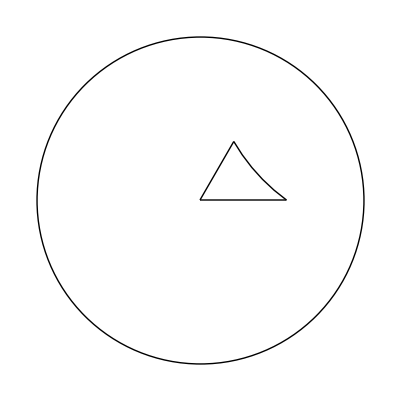

```mathematica
(* we can try to plot the hyperbolic triangle *)
Block[{α=3,β=3,γ=5,triangle,v1,v2,v3,poincareDisk=Circle[]},
	{v1,v2,v3}=phi[α,β,γ]/@{0,Infinity,1};
	triangle={findGeodesic[v1,v2],findGeodesic[v1,v3],findGeodesic[v2,v3]};
	Graphics[{
	poincareDisk,
	triangle
}]
]
```

These hyperbolic triangles are fundamental domains of triangle groups. And one can construct a lot of (but probably not all) co-compact Fuchsian groups by looking at the subgroup of triangle groups. You can build their fundamental domain by gluing multiple hyperbolic triangles together. 
If you put glue two hyperbolic triangles together along the horizontal edge, you get a fundamental domain of the Von Dyck group.

```mathematica
vD[α_,β_,γ_]:=Module[{v1,v2,v3,v4},{v1,v2,v3}=phi[α,β,γ]/@{0,Infinity,1};
v4=Conjugate[v2];
{findGeodesic[v1,v2],findGeodesic[v1,v3],findGeodesic[v2,v3],findGeodesic[v1,v4],findGeodesic[v3,v4]}
];
verticesVD[α_,β_,γ_]:=(phi[α,β,γ]/@{0,Infinity,1})~Join~{Conjugate[phi[α,β,γ][Infinity]]}
```

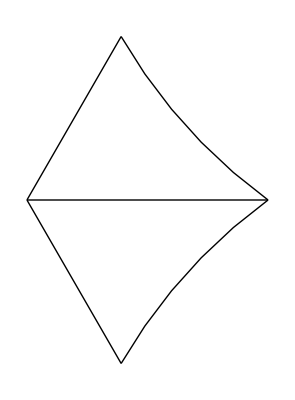

```mathematica
vD[3,3,5]//Graphics
```

the von Dyck groups can be generated by a reflection against one of the four edges, concatenated  by a reflection against the horizontal edge in the middle. If you combine these two reflections you get a rotation around one of the vertices.

Load the explicit generators from another file 
	Given a name of the orbifold, dirichletDomain[name] returns an association with

```mathematica
(* 
	Load the explicit generators from another file 
*)
<<"../src/OrbifoldData.m"
```

```mathematica
(* to get the generators for, say, [0;3,3,5], just do*)
dirichletDomain[HyperbolicTriangle[3,3,5]]["SidePairings"]
```

{{{-1/2,(√3)/2},{-(√3)/2,-1/2}},{{-1/2,-(√3)/2},{(√3)/2,-1/2}},{{1/4 (-1-√5)-2 √(1/3 (1/2+Cos[(2 π)/15]) (1/2-Sin[π/30])),(2 (1/2+1/8 (1+√5)))/(√3)},{-(2 (1/2+1/8 (1+√5)))/(√3),1/4 (-1-√5)+2 √(1/3 (1/2+Cos[(2 π)/15]) (1/2-Sin[π/30]))}},{{1/4 (-1-√5)+2 √(1/3 (1/2+Cos[(2 π)/15]) (1/2-Sin[π/30])),-(2 (1/2+1/8 (1+√5)))/(√3)},{(2 (1/2+1/8 (1+√5)))/(√3),1/4 (-1-√5)-2 √(1/3 (1/2+Cos[(2 π)/15]) (1/2-Sin[π/30]))}}}

```mathematica
(* Note that the matrices in OrbifoldData.m are all SL(2,R) matrices. If we want to make plots using the disk model, we need to conjugate the SL(2,R) matrices into SU(1,1) *)
```

```mathematica
plane2Disk[matrix_]:={{1/2,-ⅈ/2},{-ⅈ/2,1/2}}.matrix.Inverse[{{1/2,-ⅈ/2},{-ⅈ/2,1/2}}];
transformedVertices[list_][baseVertices_List]:=Module[{},
		transformBySingleMatrix[matrix_]:=
				(LinearFractionalTransform[matrix][{#1}]&)/@baseVertices//Flatten//Chop//Return;
		Return[transformBySingleMatrix/@list]
	]
```

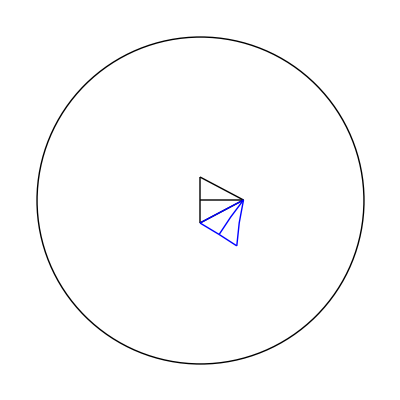

```mathematica
Block[{edgeFromVertices,generators},
	generators=dirichletDomain[HyperbolicTriangle[2,3,7]]["SidePairings"];
	edgeFromVertices=
		{
		findGeodesic[#[[1]],#[[2]]],findGeodesic[#[[1]],#[[3]]],
		findGeodesic[#[[2]],#[[3]]],findGeodesic[#[[1]],#[[4]]],
		findGeodesic[#[[3]],#[[4]]]
	}&;
	Graphics[{
			poincareDisk,
			vD[2,3,7],
			Blue,
		edgeFromVertices/@transformedVertices[plane2Disk/@generators[[4;;4]]][verticesVD[2,3,7]]
}
]
]
```

```mathematica
(* One can tessellate the whole disk by continuously attaching neighboring translates  
*)
```

```mathematica
spread[n_][list_]:=If[
n==0,
	Return[SetPrecision[{{{1,0},{0,1}}},500]],
	Return[spread[n-1][list]
		~Join~
		(Outer[Simplify[(#1.#2)]&,list,spread[n-1][list],1]//Flatten[#,1]&)//DeleteDuplicates
		]
];
```

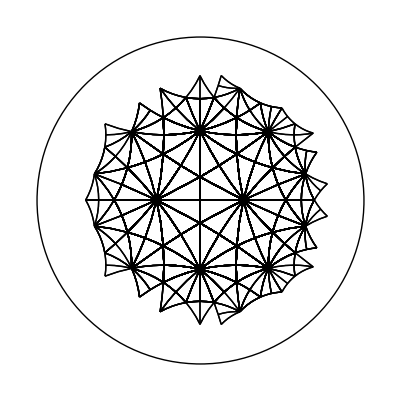

```mathematica
Block[{α=2,β=3,γ=7,generators,baseVertices,vertexList,edgeFromVertices, numOfLayers=6},
		generators=dirichletDomain[HyperbolicTriangle[α,β,γ]]["SidePairings"];
		baseVertices=verticesVD[α,β,γ];
		vertexList=
			transformedVertices[plane2Disk/@spread[numOfLayers][generators]][baseVertices];
		
		edgeFromVertices=
				{
				findGeodesic[#[[1]],#[[2]]],findGeodesic[#[[1]],#[[3]]],
				findGeodesic[#[[2]],#[[3]]],findGeodesic[#[[1]],#[[4]]],
				findGeodesic[#[[3]],#[[4]]]
			}&;

		Graphics[{
				poincareDisk,
				vD[α,β,γ],
				edgeFromVertices/@vertexList
			}]
]
```

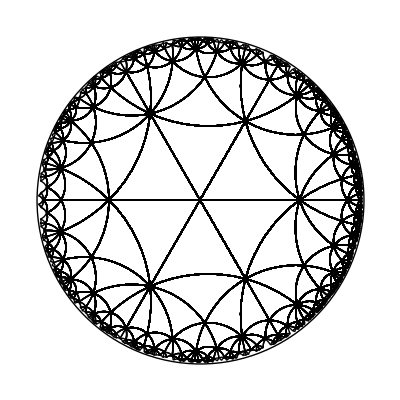

```mathematica
Block[{α=3,β=4,γ=5,generators,baseVertices,vertexList,edgeFromVertices, numOfLayers=6},
		generators=dirichletDomain[HyperbolicTriangle[α,β,γ]]["SidePairings"];
		baseVertices=verticesVD[α,β,γ];
		vertexList=
			transformedVertices[plane2Disk/@spread[numOfLayers][generators]][baseVertices];
		
		edgeFromVertices=
				{
				findGeodesic[#[[1]],#[[2]]],findGeodesic[#[[1]],#[[3]]],
				findGeodesic[#[[2]],#[[3]]],findGeodesic[#[[1]],#[[4]]],
				findGeodesic[#[[3]],#[[4]]]
			}&;

		Graphics[{
				poincareDisk,
				vD[α,β,γ],
				edgeFromVertices/@vertexList
			}]
]
```

### Bolza

For Bolza surface, the most frequently used fundamental domain is a hyperbolic octagon centered at the origin. This fundamental domain also happens to be a Dirichlet domain if the reference point is the origin ( it is nice to work with Dirichlet domains for purposes of enumerating conjugacy classes ).
By definition of the Dirichlet domain, the eight edges of the octagon are isometric circles of the side pairing generators. Note that the side pairing generators are different from the usual “algebraic topology textbook generator” in that they do not take you from one vertex to a neighbouring vertex:

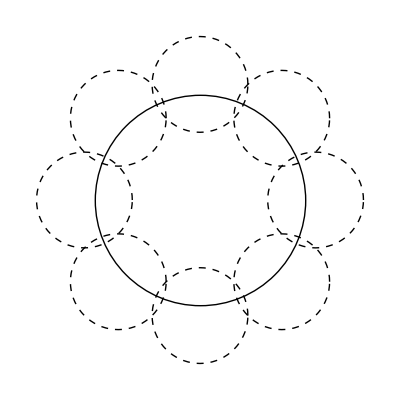

```mathematica
Graphics[{
	poincareDisk,
	Dashed,
	isometricCircle/@plane2Disk/@dirichletDomain["Bolza"]["SidePairings"]
}]
```

```mathematica
(* Plot the fundamental domain for Bolza *)
```

```mathematica
Block[{blozaIsoCircles ,intersections,innerIntersections,sortedIntersections},
	blozaIsoCircles=isometricCircle/@plane2Disk/@dirichletDomain["Bolza"]["SidePairings"]//FullSimplify;
	intersections=RegionIntersection@@#&/@zip[bolzaIsoCircles,RotateLeft[bolzaIsoCircles]]//FullSimplify;
	innerIntersections=
	SetPrecision[
		intersections/.Point[{p1__,p2__}]:>
		If[Norm[p1]<Norm[p2],
			p1[[1]]+I p1[[2]],
			p2[[1]]+I p2[[2]]
		]//FullSimplify
		,100
	];
	sortedIntersections=SortBy[innerIntersections,Arg];
	Print[sortedIntersections];
Graphics[{
poincareDisk,
findGeodesic[#[[1]],#[[2]]]&/@zip[sortedIntersections,RotateLeft[sortedIntersections]]

}]
]
```

```mathematica
(* Looking at translates *)
```

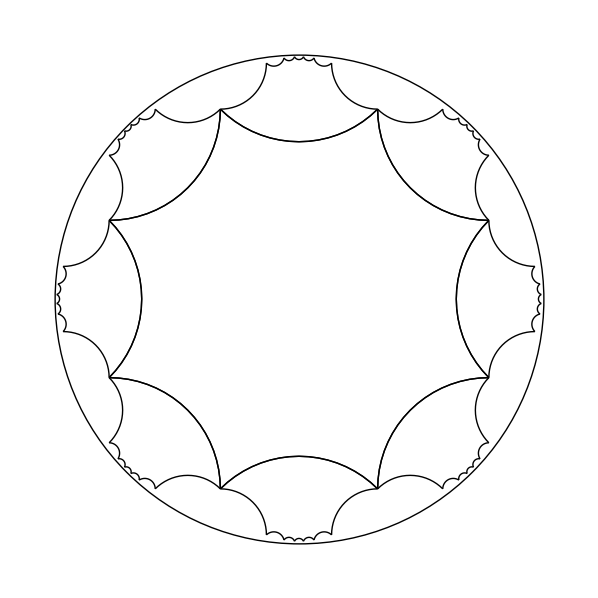

```mathematica
Block[{generators,edgeFromVertices,baseVertices,translated,edges,id},
	generators=dirichletDomain["Bolza"]["SidePairings"];
(*generators=spread[4]@dirichletDomain["Bolza"]["SidePairings"];*)
	edgeFromVertices[vertices_]:=findGeodesic[#[[1]],#[[2]]]&/@zip[vertices,RotateLeft[vertices]];
								baseVertices={-√(-1/2+ⅈ/2),√(-1/2-ⅈ/2),√(1/2-ⅈ/2),√(1/2+ⅈ/2),√(-1/2+ⅈ/2),(-1)^(5/8)/2^(1/4),(-1)^(7/8)/2^(1/4),-√(1/2+ⅈ/2)}//SetPrecision[#,100]&;
translated=transformedVertices[plane2Disk/@generators][baseVertices];

Graphics[{
poincareDisk,
edgeFromVertices@baseVertices,
edgeFromVertices/@translated
}]
]
```

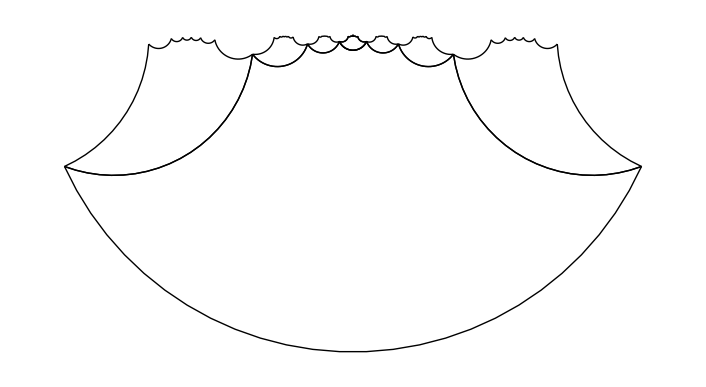

```mathematica
Block[{generators,edgeFromVertices,baseVertices,translated,edges,id},
	generators=
			(MatrixPower[dirichletDomain["Bolza"]["SidePairings"][[2]],#]&/@{5,6,7})
			~Join~
		(MatrixPower[dirichletDomain["Bolza"]["SidePairings"][[2]],5].#&/@dirichletDomain["Bolza"]["SidePairings"][[{1,2,3,4,5,7,8}]])
;
	edgeFromVertices[vertices_]:=findGeodesic[#[[1]],#[[2]]]&/@zip[vertices,RotateLeft[vertices]];
								baseVertices={-√(-1/2+ⅈ/2),√(-1/2-ⅈ/2),√(1/2-ⅈ/2),√(1/2+ⅈ/2),√(-1/2+ⅈ/2),(-1)^(5/8)/2^(1/4),(-1)^(7/8)/2^(1/4),-√(1/2+ⅈ/2)}//SetPrecision[#,100]&;
translated=transformedVertices[plane2Disk/@generators][baseVertices];

Graphics[{
edgeFromVertices/@translated
}]
]
```